## Plasma model

### Equations

```mathematica
-Graphics-;
```

```mathematica
;
```

```mathematica
;
```

### Constantes

#### Limpar

```mathematica
Clear[ϵ0,c,npa,npe,rpa,rpe]
```

#### Definir

```mathematica
ϵ0=8.8541878188 10^-12;
c=299792458;
npa=0.7;
npe=0.15;
rpe=1 10^-9;
rpa=2 10^-9;
ωp=10^10;
γ=0;
```

### Integral analítica

```mathematica
A=1/(9 π c^6(4 π ϵ0)^2)4 π ϵ0 (rpa rpe^2)/6(npe-npa)/(npe npa)
```

-7.64499×10^-70

```mathematica
epsilon[ω_,ωp_,γ_]:=1-ωp^2/(ω(ω+I ω γ))
delta[ω_,ωp_,γ_]:=(epsilon[ω,ωp,γ]-1)^2/((epsilon[ω,ωp,γ]-1+1/npa)(epsilon[ω,ωp,γ]-1+1/npe))
```

```mathematica
Γ[Ω_]:=A NIntegrate[ω^3 Abs[ω-2 Ω]^3 Abs[delta[ω-Ω,ωp,γ]]^2,{ω,0,2 Ω}]
```

```mathematica
Γ[10^6]
```

-6.98971×10^-28

```mathematica
Plot[Re[epsilon[ω,ωp,γ]],{ω,10^8,10^16}]
```

-Graphics-

### Emissão

```mathematica
Γ[Ω_,ωp_]:=1/(9 π)1/(c^6(4π ϵ)^2)(4π ϵ (rpa rpe^2)/6(npe-npa)/(npe npa))^2-1/(2 (npa-npe)^3)npa^2 npe^2 ωp^4 (4 npa Ω-4 npe Ω+npa^(3/2) ωp ArcTan[(2 Ω)/(√npa ωp)]+3 √npa npe ωp ArcTan[(2 Ω)/(√npa ωp)]-3 npa √npe ωp ArcTan[(2 Ω)/(√npe ωp)]-npe^(3/2) ωp ArcTan[(2 Ω)/(√npe ωp)]-2 npa Ω Log[npa]-2 npe Ω Log[npa]+2 npa Ω Log[npe]+2 npe Ω Log[npe]+2 npa Ω Log[4 Ω^2+npa ωp^2]+2 npe Ω Log[4 Ω^2+npa ωp^2]-2 npa Ω Log[4 Ω^2+npe ωp^2]-2 npe Ω Log[4 Ω^2+npe ωp^2])
```

### Plot em função de Ω e ω_p

```mathematica
ωpOrderMin=9;
ωpOrderMax=13;
Ωmin=10^7;
Ωmax=10^14;
(*wpValues=Array[#1&,10,{ωpMin,ωpMax}];*)
wpValues=Table[10^n,{n,ωpOrderMin,ωpOrderMax}];
legends=Table["ω_p="ScientificForm[N[wpValues[[i]]]],{i,Dimensions[wpValues.08][[1]]}]
```

{ω_p= (1.×10^9),ω_p= (1.×10^10),ω_p= (1.×10^11),ω_p= (1.×10^12),ω_p= (1.×10^13)}

```mathematica
plots=LogLogPlot[Table[Γ[Ω,ωp],{ωp,wpValues}]//Evaluate,{Ω,Ωmin,Ωmax},GridLines->Automatic,PlotLegends->legends,AxesLabel->{"Ω(Hz)","Γ(photon/s)"}];
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["plasmaPlot.png",plots]
```

G:\Outros computadores\Meu computador\Lucas 2024\UFRJ\Mestrado\DCE

plasmaPlot.png

#### Strange Behavior low Ω

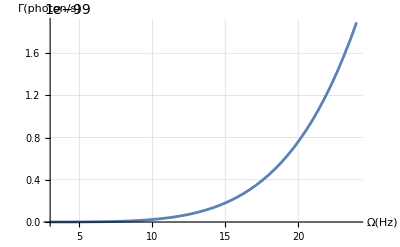

```mathematica
Plot[Γ[Ω,10000],{Ω,3,24},GridLines->Automatic,AxesLabel->{"Ω(Hz)","Γ(photon/s)"}]
```